```mathematica
path=NotebookDirectory[];
```

```mathematica
data=Import[path<>"pubmeddata.txt","Table"]
```

{{2009,231},{2010,192},{2008,191},{2007,187},{2006,186},{2004,127},{2005,114},{2002,79},{2003,74},{2000,64},{1996,49},{1999,46},{2001,45},{1997,40},{1995,38},{1994,38},{1998,36},{1991,34},{1990,30},{1992,27},{1993,21},{1980,21},{1989,21},{1973,20},{1977,18},{1985,17},{1986,17},{1979,17},{1987,17},{1983,17},{1974,16},{1984,16},{1972,16},{1988,15},{1982,15},{1981,15},{1968,15},{1975,14},{1978,14},{1971,9},{1969,7},{1976,5},{1970,3},{1967,2},{1965,2},{1953,1}}

```mathematica
data//MatrixForm
```

(2009 | 231
2010 | 192
2008 | 191
2007 | 187
2006 | 186
2004 | 127
2005 | 114
2002 | 79
2003 | 74
2000 | 64
1996 | 49
1999 | 46
2001 | 45
1997 | 40
1995 | 38
1994 | 38
1998 | 36
1991 | 34
1990 | 30
1992 | 27
1993 | 21
1980 | 21
1989 | 21
1973 | 20
1977 | 18
1985 | 17
1986 | 17
1979 | 17
1987 | 17
1983 | 17
1974 | 16
1984 | 16
1972 | 16
1988 | 15
1982 | 15
1981 | 15
1968 | 15
1975 | 14
1978 | 14
1971 | 9
1969 | 7
1976 | 5
1970 | 3
1967 | 2
1965 | 2
1953 | 1)

```mathematica
datas=SortBy[data,First]
```

{{1953,1},{1965,2},{1967,2},{1968,15},{1969,7},{1970,3},{1971,9},{1972,16},{1973,20},{1974,16},{1975,14},{1976,5},{1977,18},{1978,14},{1979,17},{1980,21},{1981,15},{1982,15},{1983,17},{1984,16},{1985,17},{1986,17},{1987,17},{1988,15},{1989,21},{1990,30},{1991,34},{1992,27},{1993,21},{1994,38},{1995,38},{1996,49},{1997,40},{1998,36},{1999,46},{2000,64},{2001,45},{2002,79},{2003,74},{2004,127},{2005,114},{2006,186},{2007,187},{2008,191},{2009,231},{2010,192}}

```mathematica
datas//MatrixForm
```

(1953 | 1
1965 | 2
1967 | 2
1968 | 15
1969 | 7
1970 | 3
1971 | 9
1972 | 16
1973 | 20
1974 | 16
1975 | 14
1976 | 5
1977 | 18
1978 | 14
1979 | 17
1980 | 21
1981 | 15
1982 | 15
1983 | 17
1984 | 16
1985 | 17
1986 | 17
1987 | 17
1988 | 15
1989 | 21
1990 | 30
1991 | 34
1992 | 27
1993 | 21
1994 | 38
1995 | 38
1996 | 49
1997 | 40
1998 | 36
1999 | 46
2000 | 64
2001 | 45
2002 | 79
2003 | 74
2004 | 127
2005 | 114
2006 | 186
2007 | 187
2008 | 191
2009 | 231
2010 | 192)

```mathematica
Length[datas]
```

46

```mathematica
pubs=Table[datas⟦i⟧⟦2⟧,{i,1,Length[datas]}]
```

{1,2,2,15,7,3,9,16,20,16,14,5,18,14,17,21,15,15,17,16,17,17,17,15,21,30,34,27,21,38,38,49,40,36,46,64,45,79,74,127,114,186,187,191,231,192}

```mathematica
yaxislabel=Table[datas⟦i⟧⟦1⟧,{i,1,Length[datas]}]
```

{1953,1965,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010}

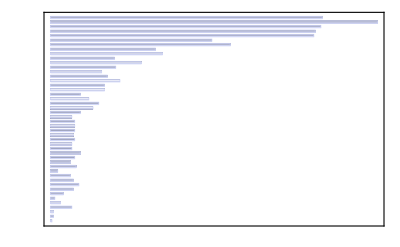

```mathematica
BarChart[pubs,ChartElementFunction->"GlassRectangle",Frame->True,BarSpacing->1,BarOrigin->Left,FrameTicks->{{yaxislabel,None},{None,None}}]
```

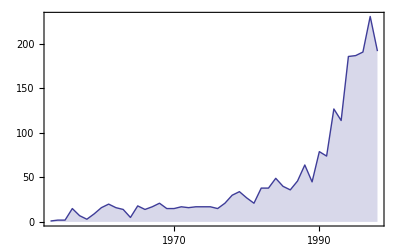

```mathematica
DateListPlot[pubs,{{1953,1,1},Automatic,"Year"},Filling->Bottom,Joined->True,FrameStyle->Directive[Black,Thickness[0.001]]]
```

```mathematica
Export[path<>"pubmeddata.pdf",%]
```

/Volumes/chaitanyagokhale/Documents/Thesis_Template/Thesis/draft_05/EGTfigs/pubmeddata.pdf